```mathematica
Psi[x]:=Exp[I*x*k]*Exp[I*h*k^2*t/(2m)]/Sqrt[L];
```

```mathematica
o1=Integrate[1/Sqrt[L]*Cos[k*z-w1*t]*Exp[I*z*k]*Exp[I*h*k^2*t/(2m)]/Sqrt[L],{z,0,L}]//Expand
```

1/2 ⅇ^(2 ⅈ t w1+(ⅈ t (h k^2-2 m w1))/(2 m))+(ⅈ ⅇ^((ⅈ t (h k^2-2 m w1))/(2 m)))/(4 k L)-(ⅈ ⅇ^(2 ⅈ k L+(ⅈ t (h k^2-2 m w1))/(2 m)))/(4 k L)

```mathematica
1/2 ⅇ^(2 ⅈ t w1+(ⅈ t (h k^2-2 m w1))/(2 m))//FullSimplify
```

1/2 ⅇ^((ⅈ t (h k^2+2 m w1))/(2 m))

```mathematica
o1=Integrate[1/Sqrt[L]*Exp[-I*k*z]*Exp[I*z*k]*Exp[I*h*k^2*t/(2m)]/Sqrt[L],{z,0,L}]//FullSimplify
```

ⅇ^((ⅈ h k^2 t)/(2 m))

```mathematica
(ⅈ ⅇ^((ⅈ t (h k^2-2 m w1))/(2 m)))/(4 k L)//FullSimplify
```

(ⅈ ⅇ^((ⅈ t (h k^2-2 m w1))/(2 m)))/(4 k L)

```mathematica
oo1=FullSimplify[Abs[o1],Assumptions->{k>0,x>0,h>0,t>0,m>0,L>0}]
```

Abs[Sin[k L]]/(k L)

```mathematica
o2=Integrate[(Exp[-I*z*k]*Exp[-I*h*k^2*t/(2m)]/Sqrt[L])
*Cos[-k*z-(w1+Dw)t]*Exp[2*I*z*k]*Exp[I*h*2^2*k^2*t/(2m)]/Sqrt[L],{z,0,L}]//FullSimplify
```

(ⅇ^(1/2 ⅈ t ((3 h k^2)/m-2 (Dw+w1))) (-ⅈ ⅇ^(2 ⅈ t (Dw+w1)) (-1+ⅇ^(2 ⅈ k L))+2 k L))/(4 k L)

```mathematica
(ⅇ^(1/2 ⅈ t ((3 h k^2)/m-2 (Dw+w1))) (+2 k L))/(4 k L)//FullSimplify
```

1/2 ⅇ^(1/2 ⅈ t ((3 h k^2)/m-2 (Dw+w1)))

```mathematica
oR=dipole^2/4*(1/2 ⅇ^(1/2 ⅈ t ((3 h k^2)/m-2 (Dw+w1)))*1/2 ⅇ^((ⅈ t (h k^2+2 m w1))/(2 m)))/(2delta)//FullSimplify
```

(dipole^2 ⅇ^(-ⅈ (Dw-(2 h k^2)/m) t))/(32 delta)

```mathematica
E1=Cos[k*z-w1*t];
```

```mathematica
E2=Cos[-k*z-(w1+Dw)*t];
```

```mathematica
(E1+E2)^2
```

(Cos[t w1-k z]+Cos[t (Dw+w1)+k z])^2

```mathematica
Integrate[1/Sqrt[L]
*(Cos[t w1-k z]+Cos[t (Dw+w1)+k z])^2*Exp[2*I*z*k]*Exp[I*h*2^2*k^2*t/(2m)]/Sqrt[L],{z,0,L}]//FullSimplify
```

(ⅇ^(-ⅈ (Dw-(2 h k^2)/m) t) (-ⅈ ⅇ^(ⅈ Dw t) (-1+ⅇ^(2 ⅈ k L)) (4+ⅇ^(ⅈ Dw t) (1+ⅇ^(2 ⅈ k L)))+4 k L) Cos[1/2 t (Dw+2 w1)]^2)/(4 k L)

```mathematica
(ⅇ^(-ⅈ (Dw-(2 h k^2)/m) t) (4 k L) Cos[1/2 t (Dw+2 w1)]^2)/(4 k L)//FullSimplify
```

ⅇ^(-ⅈ (Dw-(2 h k^2)/m) t) Cos[1/2 t (Dw+2 w1)]^2

```mathematica
Integrate[Cos[x]^2,{x,0,2Pi}]/(2Pi)
```

1/2

```mathematica
FullSimplify[Abs[oR],Assumptions->{k>0,x>0,h>0,t>0,m>0,L>0}]
```

Abs[Sin[k L]]/(k L)

```mathematica
2-2 Cos[k L]-4Sin[k*L/2]^2//FullSimplify
```

0

```mathematica
Integrate[w1^3(wba-w1)^3*(a0^2*(1/w1+1/(wba-w1)))^2,{w1,0,wba}]
```

(a0^4 wba^5)/6

```mathematica
numbers={e->1.602*10^(-19),
a0->5.29*10^(-11),
wba->2*Pi*3*10^8/(121.55313039215687*10^(-9)),
hbar->1.055*10^(-34),
c->3*10^8};
```

```mathematica
A=(1/2)*8*e^4*a0^4*wba^5/(3*Pi*hbar^2*c^6*6)/.numbers
```

4.0323×10^-20

```mathematica
1/A
```

2.47997×10^19

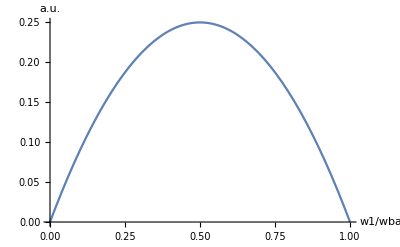

```mathematica
Plot[w1^3*(1-w1)^3*(1/w1+1/(1-w1))^2,{w1,0,1},Ticks->{True,False},AxesLabel->{"w1/wba","a.u."}]
```

```mathematica
Integrate[Cos[k*z-w*t],{t,0,2Pi}]
```

(2 Cos[π w-k z] Sin[π w])/w

```mathematica
Integrate[(1/Sqrt[L])*(Cos[k*z]^2)*(Exp[2*I*z*k]*Exp[I*h*2^2*k^2*t/(2m)]/Sqrt[L]),{z,0,L}]//FullSimplify
```

-(ⅈ ⅇ^((2 ⅈ h k^2 t)/m) (-5+4 ⅇ^(2 ⅈ k L)+ⅇ^(4 ⅈ k L)+4 ⅈ k L))/(16 k L)